# “Popularity versus similarity in growing networks”

```mathematica
ClearAll["Global `*"];  (* czyszczenie jądra programu ze wszystkich zmiennych *)
```

### Parametry symulacji

```mathematica
nmax=500; (* liczba węzłów sieci *)
m=4;(* liczba najbliższych sąsiadów *)
```

### Definicje funkcji

#### Ramka obszaru do rysowania mapy

```mathematica
ramka[n_]:={Thickness[0.005],Black,Line[{{-n,-n},{n,-n},{n,n},{-n,n},{-n,-n}}]}
```

#### Odległość w metryce hiperbolicznej

```mathematica
dist[n_,m_]:={
d1=Abs[phi[[n]]-phi[[m]]]; (* odległość kątowa pomiędzy punktami *)
d2=Abs[phi[[n]]-phi[[m]]+2 Pi]; (* dopełnienie odległości do kąta pełnego *)
Log[n]+Log[m]+Log[Min[d1,d2]/2] (* logarytm odległosci hiperbolicznej *)
}
```

#### Znajdowanie indeksu m-tego punktu względem odległości od punktu q

```mathematica
mthInDistance[q_,m_]:=Sort[Table[{{i,phi[[i]]},dist[i,q]},{i,1,q}],#1[[2]][[1]]<#2[[2]][[1]]&][[m+1]][[1]][[1]]
(* dla danego elementu q wyznaczamy posortowaną rosnąco indeksowaną tablicę odległości w metryce hiperbolicznej;zależność od kąta jako element tablicy jest potrzebna do wyznaczenia odległości pomiędzy punktmami;zwracamy indeks (m+1)-go elementu wliczając dany punkt startowy *)
```

### Parametryzacja punktów na okręgu

```mathematica
phi=Table[2 Pi Random[],{n,nmax}]; (* tablica losowych kątów *)
pos=Table[{Log[n]*Cos[phi[[n]]],Log[n]*Sin[phi[[n]]]},{n,nmax}]; (* współrzędne punktów w skali logarytmicznej *)
size=Table[2,{n,nmax}]; (* wielkość powstającego wierzchołka rysowanego na mapie *)
```

### Wyznaczanie połączeń pomiędzy wierzchołkami

```mathematica
dists={}; (* inicjalizacja pustej listy odległości *)
e={}; (* inicjalizacja pustej listy krawędzi *)
For[i=1,i≤nmax,i++,
For[j=1,j≤m,j++,
If[j≥i,, (* dla j≥i nie rób nic *)
x1=pos[[i]]; (* współrzędne i-tego wierzchołka *)
mth=mthInDistance[i,j]; (* indeks s-tego wierzchołka względem odległości oc i-tego *)
x2=pos[[mth]]; (* współrzędne s-tego wierzchołka względem odległości od i-tego *)
AppendTo[dists,dist[i,j]]; (* dodanie nowej odległości do istniejącej listy *)
AppendTo[e,{Line[{x1,x2}]}]; (* dodanie nowej krawędzi do zbioru istniejących *)
size[[mth]]++ (* zwiększenie rozmiaru wierzchołka w miarę kolejnych połączeń *)
] 
] 
];
```

### Rysowanie mapy dla metryki hiperbolicznej

```mathematica
v=Table[{PointSize[0.012 Log[size[[n]]]],RGBColor[1-.1Log[size[[n]]],1-.25Log[size[[n]]],1-.65Log[size[[n]]]],Point[{Log[n]*Cos[phi[[n]]],Log[n]*Sin[phi[[n]]]}]},{n,nmax}]; (* wierzchołki *)
box=ramka[Log[nmax+1]]; (* wielkość obszaru ramki *)
circle=Table[{Blue,Dashed,Circle[{0,0},Log[n]]},{n,1,nmax,nmax/20}]; (* okręgi wyznaczające czas powstania wierzchołka *)
Show[Graphics[{box,circle,e,v}],ImageSize->600]
```

-Graphics-

### Galeria obrazków dla różnych parametrów (n_max, m)

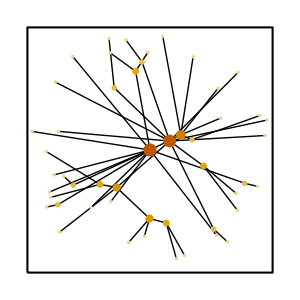
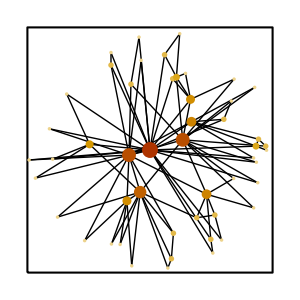
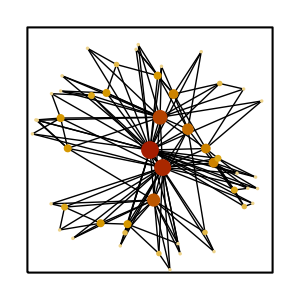
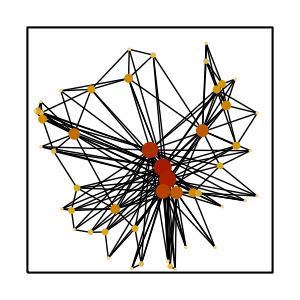
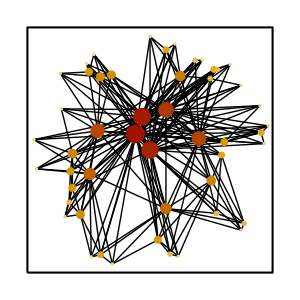
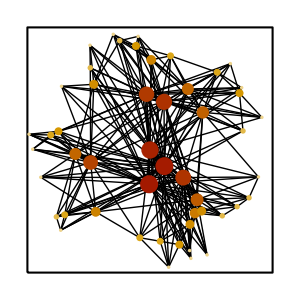
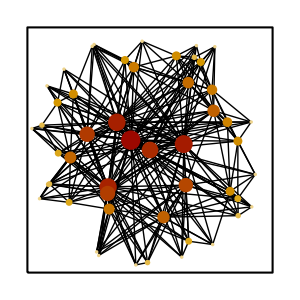
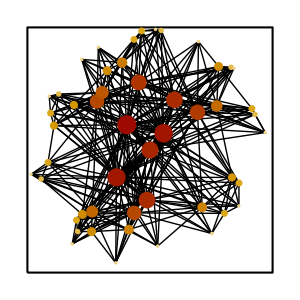
#### nmax = 50, m = {1, ..., 8} -Graphics--Graphics--Graphics--Graphics- -Graphics--Graphics--Graphics--Graphics-

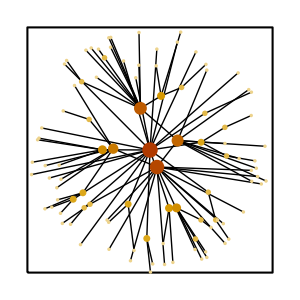
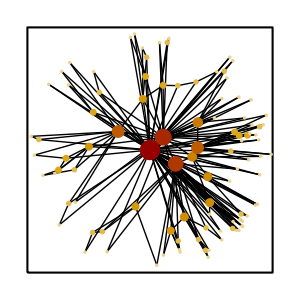
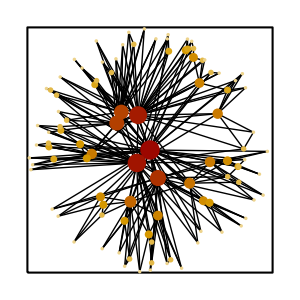
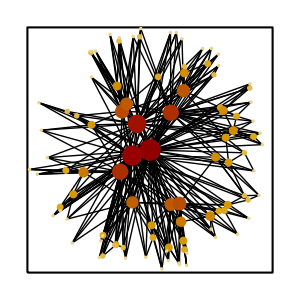
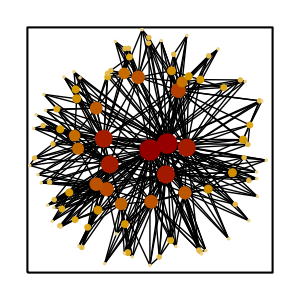
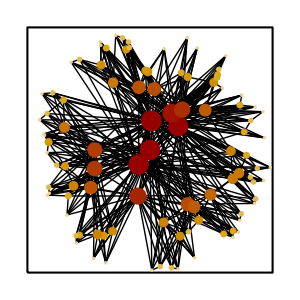
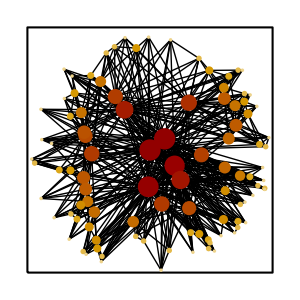
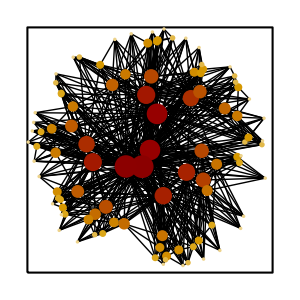
#### nmax = 100, m = {1, ..., 8} -Graphics--Graphics--Graphics--Graphics- -Graphics--Graphics--Graphics--Graphics-

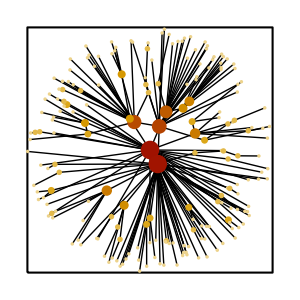
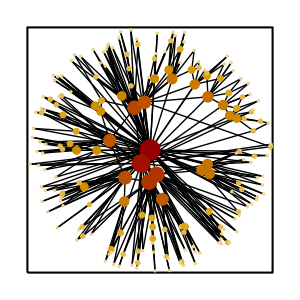
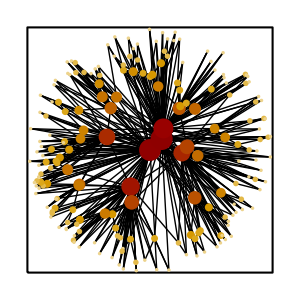
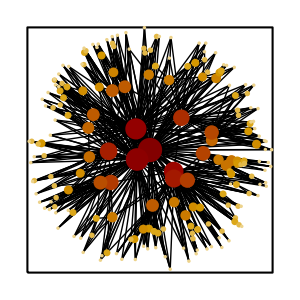
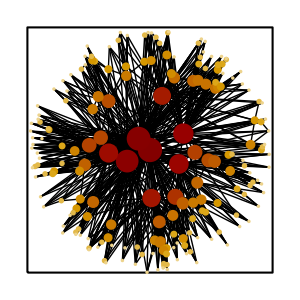
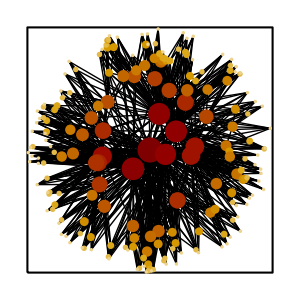
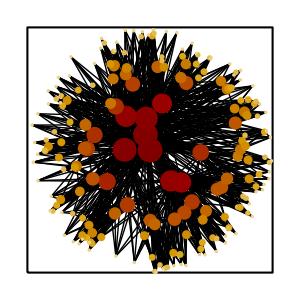
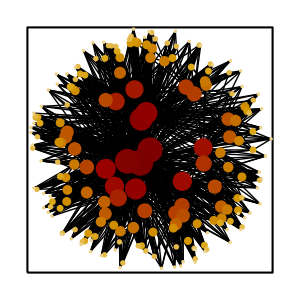
#### nmax = 200, m = {1, ..., 8} -Graphics--Graphics--Graphics--Graphics- -Graphics--Graphics--Graphics--Graphics-